## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
nuediff37={#[[1]],#[[2]]/10^(31)}&/@Transpose@N@Import["garching-data/nuediff37array.csv"];
```

```mathematica
nuediff37Red = (DeleteDuplicates@nuediff37)[[;;;;2]];
```

The data is in unit of 10^(31) cm^(-3)

```mathematica
spectFunRaw = Interpolation[nuediff37Red]
```

InterpolatingFunction[{{-1., 1.}}, <>]

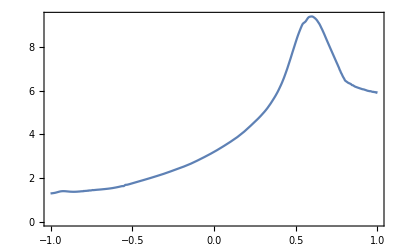

```mathematica
Plot[spectFunRaw[x],{x,-1,1},Frame->True,AxesOrigin->{0,0},Axes->False]
```

```mathematica
spectFun[u_]=CoefficientList[
Fit[nuediff37Red,Table[u^n,{n,0,20}],u],
u].Table[u^n,{n,0,20}]
```

3.1091+3.94885 u+13.6321 u^2+29.7702 u^3-225.442 u^4-633.296 u^5+2004.45 u^6+6141.36 u^7-7352.7 u^8-27716.9 u^9+11634.1 u^10+67595. u^11-3020.74 u^12-95880.5 u^13-16046.9 u^14+79560.6 u^15+24007.7 u^16-35942.6 u^17-14192.4 u^18+6845.04 u^19+3178.78 u^20

```mathematica
CForm[
3.1091047622370787+3.948849723450116 u+13.632133984410414 u^2+29.7701637868053 u^3-225.4418693733076 u^4-633.2956958542956 u^5+2004.4496383988198 u^6+6141.363460150786 u^7-7352.704265944309 u^8-27716.899615370356 u^9+11634.107295351703 u^10+67594.95724260398 u^11-3020.7355985575978 u^12-95880.52468537232 u^13-16046.882567924806 u^14+79560.56837894565 u^15+24007.739039308894 u^16-35942.62467824584 u^17-14192.446695305043 u^18+6845.044976045668 u^19+3178.7833154504706 u^20
]
```

3.1091047622370787 + 3.948849723450116*u + 13.632133984410414*Power(u,2) + 29.7701637868053*Power(u,3) - 
   225.4418693733076*Power(u,4) - 633.2956958542956*Power(u,5) + 2004.4496383988198*Power(u,6) + 
   6141.363460150786*Power(u,7) - 7352.704265944309*Power(u,8) - 27716.899615370356*Power(u,9) + 
   11634.107295351703*Power(u,10) + 67594.95724260398*Power(u,11) - 3020.7355985575978*Power(u,12) - 
   95880.52468537232*Power(u,13) - 16046.882567924806*Power(u,14) + 79560.56837894565*Power(u,15) + 
   24007.739039308894*Power(u,16) - 35942.62467824584*Power(u,17) - 14192.446695305043*Power(u,18) + 
   6845.044976045668*Power(u,19) + 3178.7833154504706*Power(u,20)

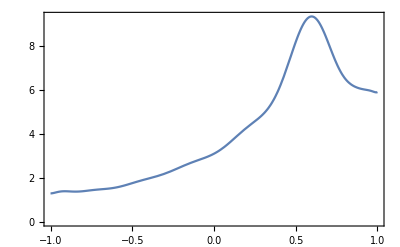

```mathematica
Plot[spectFun[x],{x,-1,1},Frame->True,AxesOrigin->{0,0},Axes->False]
```

```mathematica
SpectrumOmegaNMAA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.9,1,-1,spectFun]
SpectrumOmegaNMZA[0.999,1,-1,spectFun]
SpectrumOmegaNMZA[0.9999,1,-1,spectFun]
```

-1.3619

{-1.07968,3.80348}

{-1.87589,6.22454}

{-4.51809,9.84329}

{-5.70431,11.0595}

```mathematica
Plot[
SpectrumOmegaNMAA[n,1,-1,spectFun],
{n,-0.99,0.99}
]
```

$Aborted

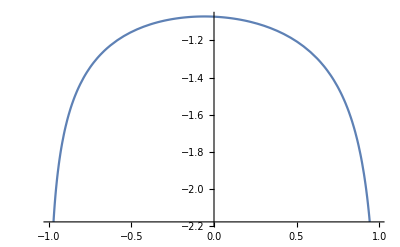

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[1]],
{n,-0.99,0.99}
]
```

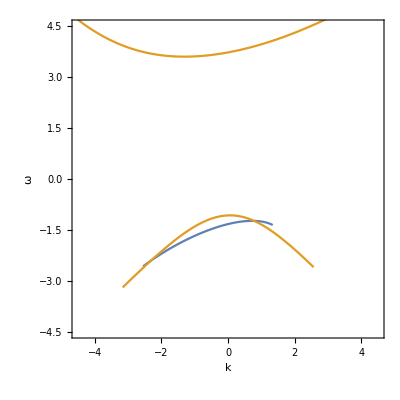

```mathematica
pltSpect=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,1,-1,spectFun],SpectrumOmegaNMAA[n,1,-1,spectFun]},
{n *#,#}&/@SpectrumOmegaNMZA[n,1,-1,spectFun]
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

```mathematica
Export["pltSpect.png",pltSpect]
```

pltSpect.png

```mathematica
??Export
```

RowBox[{"Export", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\).\!\(\*StyleBox[\"ext\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["expr", "TI"]}], "]"}] exports data to a file, converting it to the format corresponding to the file extension StyleBox["ext", "TI"]. 
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"format\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] exports data in the specified format.
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["exprs", "TI"], ",", StyleBox["elems", "TI"]}], "]"}] exports data by treating StyleBox["exprs", "TI"] as elements specified by StyleBox["elems", "TI"].
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["elems", "TI"], ",", StyleBox["relems", "TI"]}], "]"}] returns to StyleBox["the Wolfram System", "RebrandingTerm"] the elements specified by StyleBox["relems", "TI"].

Attributes[Export]={Protected,ReadProtected}

## Validate Data

```mathematica
maalsadataGarching01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/maalsadata-garching-01.csv"
];
mzaplsadataGarching01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzaplsadata-garching-01.csv"
];
mzamlsadataGarching01=Import[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzamlsadata-garching-01.csv"
];
```

```mathematica
Dimensions@maalsadataGarching01
Dimensions@mzaplsadataGarching01
Dimensions@mzamlsadataGarching01
```

{8999,3}

{900,3}

{900,3}

```mathematica
maalsadataGarching01Clean=Select[
maalsadataGarching01,10^(-10)<Abs@#[[3]]<20&&-5<#[[2]]<0&
];
Dimensions@%

mzaplsadataGarching01Clean=Select[
mzaplsadataGarching01,10^(-10)<Abs@#[[3]]<10&&#[[1]]<0&
];

Dimensions@%

mzamlsadataGarching01Clean=Select[
mzamlsadataGarching01,10^(-10)<Abs@#[[3]]<10&&#[[1]]>0&
];

Dimensions@%
```

{1231,3}

{360,3}

{107,3}

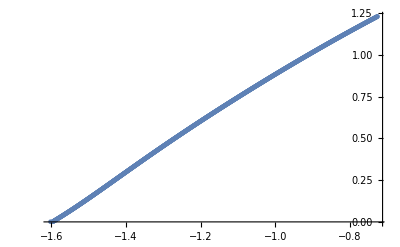

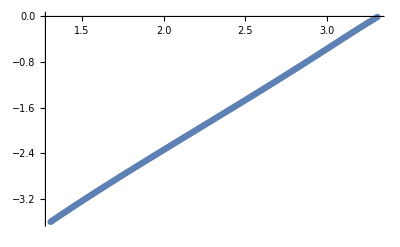

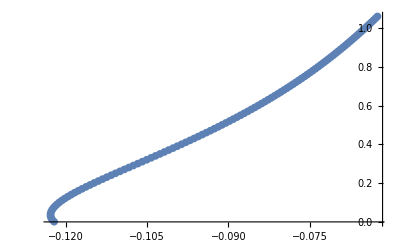

```mathematica
ListPlot[
{#[[2]],#[[1]]}&/@maalsadataGarching01Clean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzaplsadataGarching01Clean
]
ListPlot[
{#[[2]],#[[1]]}&/@mzamlsadataGarching01Clean
]
```

```mathematica
Export[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/maalsadata-garching-01-clean.csv",
maalsadataGarching01Clean
]
Export[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzaplsadata-garching-01-clean.csv",
mzaplsadataGarching01Clean
]
Export[
"/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzamlsadata-garching-01-clean.csv",
mzamlsadataGarching01Clean
]
```

/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/maalsadata-garching-01-clean.csv

/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzaplsadata-garching-01-clean.csv

/Users/leima/github/dispersion-relation-paper/program/data/dr-garching/mzamlsadata-garching-01-clean.csv

## A Fiducial Spectrum

```mathematica
spectFunTest[u]=u+0.5
```

0.5+u

```mathematica
SpectrumOmegaNMZA[0.9,1,-1,spectFunTest]
SpectrumOmegaNMZA[0.1,1,-1,spectFunTest]
SpectrumOmegaNMZA[-0.1,1,-1,spectFunTest]
SpectrumOmegaNMZA[-0.9,1,-1,spectFunTest]
```

{-0.0936019,0.723694}

{0.0917956,0.255598}

{0.160306-0.0820395 ⅈ,0.160306+0.0820395 ⅈ}

{0.110385-0.431714 ⅈ,0.110385+0.431714 ⅈ}

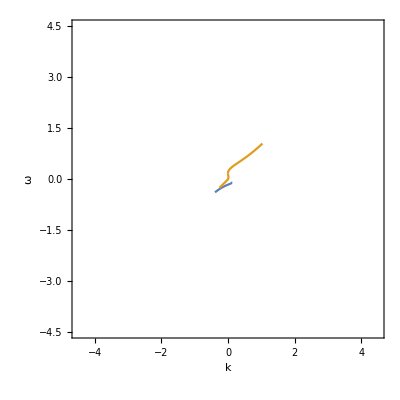

```mathematica
pltSpectTest=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,1,-1,spectFunTest],SpectrumOmegaNMAA[n,1,-1,spectFunTest]},
{n *#,#}&/@SpectrumOmegaNMZA[n,1,-1,spectFunTest]
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

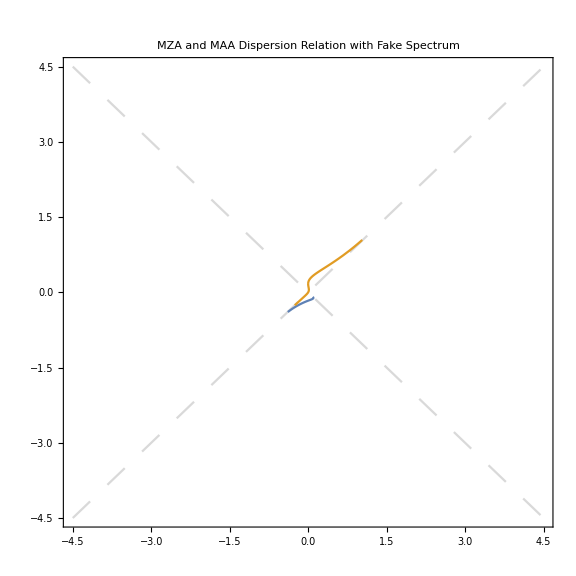

```mathematica
Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpectTest
]
```